# Introduction to MadGraph5

In this notebook you will be guided through the basics of MadGraph5. You will be invited to answer several questions, write some basic functions, and do some basic analysis of simulated collider events. Please answer every question along the way. You will know there is something for you to do or answer when you see bold text.

Let’s learn how to use MadGraph
First, navigate to the MadGraph directory, probably called something like
ls
the final numbers may be different depending on the version of the software you have

From that directory you can execute 
./bin/mg5_aMC

This should bring up a screen something like

************************************************************
*                     MadGraph5_aMC@NLO                    *
*                                                          *
*                *                       *                 *
*                  *        * *        *                   *
*                    * * * * 5 * * * *                     *
*                  *        * *        *                   *
*                *                       *                 *
*                                                          *
*                                                          *
*         VERSION 3.4.1                 2022-09-01         *
*                                                          *
*    The MadGraph5_aMC@NLO Development Team - Find us at   *
*    https://server06.fynu.ucl.ac.be/projects/madgraph     *
*                            and                           *
*            http://amcatnlo.web.cern.ch/amcatnlo/         *
*                                                          *
*               Type ‘help’ for in-line help.              *
*           Type ‘tutorial’ to learn how MG5 works         *
*    Type ‘tutorial aMCatNLO’ to learn how aMC@NLO works   *
*    Type ‘tutorial MadLoop’ to learn how MadLoop works    *
*                                                          *
************************************************************

Followed by a bunch of things you can mostly ignore. What you need to focus on is this part:

Loading default model: sm
INFO: Restrict model sm with file models/sm/restrict_default.dat . 
INFO: Run "set stdout_level DEBUG" before import for more information. 
INFO: Change particles name to pass to MG5 convention 
Defined multiparticle p = g u c d s u~ c~ d~ s~
Defined multiparticle j = g u c d s u~ c~ d~ s~
Defined multiparticle l+ = e+ mu+
Defined multiparticle l- = e- mu-
Defined multiparticle vl = ve vm vt
Defined multiparticle vl~ = ve~ vm~ vt~
Defined multiparticle all = g u c d s u~ c~ d~ s~ a ve vm vt e- mu- ve~ vm~ vt~ e+ mu+ t b t~ b~ z w+ h w- ta- ta+
MG5_aMC>

Note that MadGraph has loaded the Standard Model for you (sm) and defined some multiparticle shorthand’s for you. That is, is you input  p that includes contributions from 
g gluons
u up-quarks
c charm-quarks
d down-quarks
s strange-quarks
u~ up-anti-quark
c~ charm-anti-quarks
d~ down-anti-quarks
s~ strange-anti-quarks

j is for jet, and contains the same possible particles
l+ defines the anti-electron and anti-muon 
l- defines the electron and muon
vl are the three flavors of neutrino
vl are the anti-neutrinos

there are also 
t top-quark
b bottom-quark
ta- tau
z Z-boson
w+ W-boson
h Higgs boson

During the course you will become more familiar with these particles, you don’t need to know much of anything about them at this point.

You can access some of the documentation by typing
MG5_aMC>help

for a specific command type
MG5_amc>help <command>

## electron-positron scattering

We are going to explore how MadGraph works with a very simple process. We are going to collide an electron and a positron and produce an electron and a positron.

The command is

MG5_aMC>generate e+ e- > e+ e-

This tells MadGraph that you are interested in colliding an electron (e-) and a positron (e+) and producing an electron and a positron.
Once this has been done we need to tell MadGraph we want to start simulating events. We do this by making a directory for working in

MG5_aMC>output proc_sm_ee_ee

This command tells MadGraph to output the process that was just generated into a new directory with the name specified afterward. I’ve used this one to remind me that I am using the Standard Model (sm) with initial state ee and final state ee. But you can name your whatever you’d like. However, as we will be generating a number of directories throughout the course I recommend a descriptive name so you can find what you need later.

Go ahead and quit using the command
MG5_aMC>quit

You should now see that in your MadGraph directory (or where ever you decided to call madgraph from) there is a folder with the name of whatever you called your output. In my case the folder is called “proc_sm_ee_ee”
Inside the folder there are lots of things, but let’s focus on the folder named “Cards”
These cards are full of different parameter values that MadGraph will use when generating events
Let’s start with the run card “run_card.dat”

Scan through this. 
There are several things we can set. First,
# Warning: Do not generate more than 1M events in a single run       *
#*********************************************************************
  10000 = nevents ! Number of unweighted events requested 
  0   = iseed   ! rnd seed (0=assigned automatically=default))
#*********************************************************************
This lets us set how many event we’d like to generate. Let’s keep this at 10,000 for now. Note that since numerical methods are never truly random they don’t recommend generating more that 1 million events at once. If you need more than that make them in several 1 million event batches.
Next,
# Collider type and energy                                           *
# lpp: 0=No PDF, 1=proton, -1=antiproton, 2=photon from proton,      *
#                3=photon from electron, 4=photon from muon          *
#*********************************************************************
     0        = lpp1    ! beam 1 type 
     0        = lpp2    ! beam 2 type
     500.0     = ebeam1  ! beam 1 total energy in GeV
     500.0     = ebeam2  ! beam 2 total energy in GeV
#*********************************************************************
# Beam polarization from -100 (left-handed) to 100 (right-handed)    *
#*********************************************************************
     0.0     = polbeam1 ! beam polarization for beam 1
     0.0     = polbeam2 ! beam polarization for beam 2
 We can now set our collider type. We are considering an electron-positron collider so we leave these set to 0. For now we also leave the beams unpolarized. But what energy collider should we be using? Let’s use the low energy 
     0.5     = ebeam1  ! beam 1 total energy in GeV
     0.5     = ebeam2  ! beam 2 total energy in GeV
Question 1: With beam energies set as above, what is the center-of-momentum collider energy?
Answer: 1 GeV

We can skip a bunch of things now. Go down to 
#*******************************                                                 
# Parton level cuts definition *
#*******************************                                     
#                                                                    
#
#*********************************************************************
# BW cutoff (M+/-bwcutoff*Gamma) ! Define on/off-shell for “$” and decay  
#*********************************************************************
  15.0  = bwcutoff      ! (M+/-bwcutoff*Gamma)
#*********************************************************************
# Standard Cuts                                                      *

Let's look at this for a minute.
#*********************************************************************
# Minimum and maximum pt's (for max, -1 means no cut)                *
#*********************************************************************
 10.0  = ptl       ! minimum pt for the charged leptons 
 -1.0  = ptlmax    ! maximum pt for the charged leptons
 {} = pt_min_pdg ! pt cut for other particles (use pdg code). Applied on particle and anti-particle
 {}	= pt_max_pdg ! pt cut for other particles (syntax e.g. {6: 100, 25: 50})

We don’t want the minimum pt (this is the transverse momentum) to be 10 GeV, because the collider energy was just set to 1 GeV. If we leave this the way it is we won’t produce any events. Let’s set this to -1, that way there is no minimum value. 
So,
# Minimum and maximum pt’s (for max, -1 means no cut)                *
#*********************************************************************
 -1.0  = ptl       ! minimum pt for the charged leptons 
 -1.0  = ptlmax    ! maximum pt for the charged leptons
 {} = pt_min_pdg ! pt cut for other particles (use pdg code). Applied on particle and anti-particle
 {}= pt_max_pdg ! pt cut for other particles (syntax e.g. {6: 100, 25: 50}) 
Make sure that after you change the card file you then save it. If you don’t save the changes then they won’t be applied when you generate actual events.

This sets the minimum and maximum energies of various collider objects. The 
default is no cut, let’s leave it that way for now.
#*********************************************************************
# Minimum and maximum E's (in the center of mass frame)              *
#*********************************************************************
  0.0  = ej     ! minimum E for the jets
  0.0  = eb     ! minimum E for the b
  0.0  = ea     ! minimum E for the photons
  0.0  = el     ! minimum E for the charged leptons
  -1.0   = ejmax ! maximum E for the jets
 -1.0   = ebmax ! maximum E for the b
 -1.0   = eamax ! maximum E for the photons
 -1.0   = elmax ! maximum E for the charged leptons
 {} = e_min_pdg ! E cut for other particles (use pdg code). Applied on particle and anti-particle
 {} = e_max_pdg ! E cut for other particles (syntax e.g. {6: 100, 25: 50})

Max rapidity looks fine for now. But we should remember that we have made a cut on the rapidity. Note also that this is η which is actually the pseudorapidity. 
Question 2: Why is the |η|<2.5 cut the usual standard?
Answer: We set it below 2.5 because we only want the particles that give us interesting reactions. A large η means an angle of deflection of 0, and the tangent of 0 is 0; take the ln of that and you get essentially negative infinity. This means that these reactions do not tell us anything. Therefore, we want the reactions that actually tell us something and are under 2.5.

#*********************************************************************
# Maximum and minimum absolute rapidity (for max, -1 means no cut)   *
#*********************************************************************
 2.5  = etal    ! max rap for the charged leptons 
 0.0  = etalmin ! main rap for the charged leptons
 {} = eta_min_pdg ! rap cut for other particles (use pdg code). Applied on particle and anti-particle
 {} = eta_max_pdg ! rap cut for other particles (syntax e.g. {6: 2.5, 23: 5})
#*********************************************************************
# Minimum and maximum DeltaR distance                                *
#*********************************************************************
 0.4 = drll    ! min distance between leptons 
 -1.0  = drllmax ! max distance between leptons
 Everything else can be left as the defaults assign them. Note here we are requiring a minimum ΔR between leptons.

We have made some changes to the run card, so we need to make sure we SAVE the file with the changes or else they will not be applied when we generate events.

Now we need to look at the parameter card in param_card.dat
###################################
## INFORMATION FOR MASS
###################################
Block mass 
    5 4.700000e+00 # MB 
    6 1.730000e+02 # MT 
   15 1.777000e+00 # MTA 
   23 9.118800e+01 # MZ 
   25 1.250000e+02 # MH 
## Dependent parameters, given by model restrictions.
## Those values should be edited following the 
## analytical expression. MG5 ignores those values 
## but they are important for interfacing the output of MG5
## to external program such as Pythia.
  1 0.000000e+00 # d : 0.0 
  2 0.000000e+00 # u : 0.0 
  3 0.000000e+00 # s : 0.0 
  4 0.000000e+00 # c : 0.0 
  11 0.000000e+00 # e- : 0.0 
  12 0.000000e+00 # ve : 0.0 
  13 0.000000e+00 # mu- : 0.0 
  14 0.000000e+00 # vm : 0.0 
  16 0.000000e+00 # vt : 0.0 
  21 0.000000e+00 # g : 0.0 
  22 0.000000e+00 # a : 0.0 
  24 8.041900e+01 # w+ : cmath.sqrt(MZ__exp__2/2. + cmath.sqrt(MZ__exp__4/4. - (aEW*cmath.pi*MZ__exp__2)/(Gf*sqrt__2))) 
  
 Notice that many of the particle masses have been hard coded in as zero. 
 Question 3: Why are so many of these particles, which are known to have nonzero masses, explicitly taken to have zero mass?
 Answer: Because their mass is so small compared to the proton and other bigger particles, that it is essentially zero.

## Cross section Considerations

Okay, we are ready to generate some events!

In the directory you made, in my case the name is
proc_sm_ee_ee
we execute the following command

./bin/generate_events 2 1 proc_sm_ee_ee_1GeV_10k

This calls the generate events function the flag 2 means multicore, so I could in principle use more than once core if they are available on whatever machine I’m using. The 1 means just use one core and then I give a name to the events I’m generating. In this case I have specified the model “sm” the process “ee_mumu” the center of mass energy “1GeV” and the  number of events “10k”

(I ran into a new issue on my Mac regarding making events. For some reason in my proc directory no “Events” file was made. This is annoying, but easy to fix. Just add an empty fold named “Events” and everything should work.)

Question 4: What is the cross section generated by MadGraph, including the uncertainty
Answer: See answer below

Let’s see how this changes as we change the number of events generated. Go back and change the run card so that only 100 events are generated. Then 1,000 and 100,000. Record the cross sections below including the uncertainties. Also record the time it takes to generate the events. Remember to name each run uniquely so that you can check the individual events. (You already did the 10,000 case so you can just record that value again as part of the table.)
Table 1:
Number of Events                                    Cross section 				Total CPU time
100							3.897e+07 +- 2.449e+05 pb	2 seconds
1,000						3.923e+07 +- 1.619e+05 pb	3 seconds
10,000						3.921e+07 +- 5.082e+04 pb	9 seconds
100,000						3.921e+07 +- 1.433e+04 pb	1 minute 25 seconds
Reflection 1: Considering the calculated cross sections, their uncertainties, and the time it takes to calculate how do you feel about the 10,000 event default?
Answer: The 10,000 event default is pretty awesome. I could do 100000 events to get a better uncertainty, but other than that, the 10,000 and the 100,000 have pretty much the same cross section. Oh, and the 10,000 is more than a minute faster.

Remember that in the run card we left in place a cut on the maximum pseudorapidity.
Next, let’s see what happens as we allow for more particles at higher η. Go ahead and generate 10,000 events for each η value. (Again you already did the first case, so just record it in this table again.) Remember to name each run uniquely so that you can check the events for each case. 
Table 2:
Max η				Cross section
2.5					3.921e+07 +- 5.082e+04 pb
3.0					1.098e+08 +- 1.542e+05 pb	
5.0					6.135e+09 +- 1.212e+07 pb	
Reflection 2: You should be seeing a significant change to the cross section for these different cases. The ATLAS and CMS detectors at the LHC only have full tracking and detection up to |η| = 2.5, what does this mean about the number of produced particles that miss the detector and go down the beam pipe?
Answer: That means that there are a factor of 10^2 particles that are being missed. A pseudorapidity of 5 yields 6e+09, while a pseudorapidity of 2.5 yields 3.9e07. That is a big difference.

If we are only interested in a certain range of the detector, like the region |η|<2.5, we should focus nearer that region with the generator level cuts. Otherwise we may generate a lot of events (because of larger cross sections) that don’t correspond to the effects we are interested in. This only leaves us with a few events  with sensitivity to the effects we do care about.

## Looking at the Events

To find the events that you have generated go to the Events directory within the generated process directory
Inside you should find a folder with the names you specified when you called generate_events
Inside this folder there is a banner which includes the information related to how the events were generated and a zipped file called
unweighted_events.lhe.gz
This is then to be unzipped, leaving you with a .lhe file. (lhe stands for Les Houches Event)
re-name this so that its name is descriptive, like 
proc_sm_ee_ee_1GeV_10k_eta3.lhe
or something similar

Move a copy of two event files into the same directory as this notebook (you can also just make sure that the notebook is looking in the folder with the event files, but I find it easier to keep all the Mathematic analysis files in the folder with the notebook)
Then change your Mathematic directory to this directory also.

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\carte\OneDrive\Documents\Wolfram Mathematica\513\Project 1

The function below is just to try and keep memory in check when importing events files. I don’t really know how much of a difference it makes, but it gets called in some of the functions bellow.

```mathematica
ClearMemory:=Module[{},
Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];
];(*This is just to try and ensure memory stays somewhat in control.*)
```

Ok, go ahead and look at the event file that you generated first, with 10,000 events and |η| < 2.5. It’s got a header full of all the choices you made that led up to the events. It’s nice to have a record of this, but what you really want comes after the second </header>
You should see something like
</header>
<init>
-11 11 5.000000e-01 5.000000e-01 0 0 247000 247000 -4 1
3.918574e+07 4.901073e+04 3.918574e+07 1
<generator name=’MadGraph5_aMC@NLO’ version=’3.1.0’>please cite 1405.0301 </generator>
</init>
<event>
 4      1 +3.9185742e+07 5.00000000e-01 7.54677100e-03 1.20361500e+00
      -11 -1    0    0    0    0 +0.0000000000e+00 +0.0000000000e+00 +5.0000000000e-01 5.0000000000e-01 0.0000000000e+00 0.0000e+00 -1.0000e+00
       11 -1    0    0    0    0 -0.0000000000e+00 -0.0000000000e+00 -5.0000000000e-01 5.0000000000e-01 0.0000000000e+00 0.0000e+00 -1.0000e+00
      -11  1    1    2    0    0 -8.4979345748e-02 -4.5761208182e-03 +4.9270434331e-01 5.0000000000e-01 0.0000000000e+00 0.0000e+00 -1.0000e+00
       11  1    1    2    0    0 +8.4979345748e-02 +4.5761208182e-03 -4.9270434331e-01 5.0000000000e-01 0.0000000000e+00 0.0000e+00 -1.0000e+00
</event>
What we are really interested in is all the events. So, let’s understand the anatomy of each of these event blocks
The first line has six entries but not all of them are useful for us at present. 
(NUP, IDPRUP, XWGTUP, SCALUP, AQEDUP, AQCDUP)
NUP= number of particle entries in the event
IDPRUP= ID of the process for the event
XWGTUP= event weight
SCALUP= scale of the event in GeV
AQEDUP= the QED coupling α used in the event
AQCDUP= the QCD coupling α_s used in the event
More information is given in 
https://arxiv.org/pdf/hep-ph/0109068.pdf and https://arxiv.org/pdf/hep-ph/0609017.pdf

That wasn’t too helpful, so let’s now look at the next four lines
These 13 entries define
(IDUP, ISTUP, MOTHUP1, MOTHUP2, ICOLUP1, ICOLUP2, Px, Py, Pz, E, M, VTIMUP, SPINUP)
IDUP= particle ID according to PDG convention
ISTUP= Status code (-1:Incoming Particle, +1 Outgoing final state particle, -2 intermediate spacelike propagator, +2 intermediate resonance...)
MOTHUP1= index of first mother particle
MOTHUP1= index of second mother, or set to 0
ICOLUP1= integer tag of color flow line passing through the color of the particle
ICOLUP2= integer tag of color flow line passing through the anti-color of the particle
Px= x-component of three momentum of the particle
Py= y-component of three momentum of the particle
Pz=z-component of three momentum of the particle
E= energy of the particle
M= mass of the particle
VTIMUP= invariant lifetime cτ (distance from production to decay) in millimeters
SPINUP= cosine of the angle between the spin-vector of the particle and the 3-momentum of the decaying particle, in the lab frame. If unknown set 9

We will use a few commands to only grab what we need from each event

```mathematica
eventInfo={_,_,_,_,_,_};
decayedOrIn = {_,-1,_,_,_,_,_,_,_,_,_,_,_}  | {_,2,_,_,_,_,_,_,_,_,_,_,_};
SetOut[ event_ ]  := (DeleteCases[event,decayedOrIn,2]);
ReadLHE[rawInput_ ] := 
(
(*Search for beginning of events*)
pos=Position[rawInput,{"</init>"}][[1,1]]; 
(*Throw away header info at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
DeleteCases[Split[Drop[ rawInput, pos],#=!={"</event>"}&],{_String,___}| eventInfo,2]
);
ReadEvents[filename_]:=Module[{eventListp, eventListOutLp},
Print["Time taken to read events: ",Timing[testp=Import[filename,"Table"];][[1]]];
Timing[eventListp=ReadLHE[testp]; ]; 
(*convert raw data into readable form*)
eventListp = eventListp[[1;;(Length[eventListp]-1)]];
(*drop dummy event at end*)
eventListOutLp=SetOut[eventListp]; (*remove initial particle info*)
ClearMemory;
{eventListp, eventListOutLp}
];
```

Note that the ReadEvents function makes an array with two lists inside it.
The first contains the full event, initial particles and final particles
The second just gives the final particles, this can be more useful when the initial particle state is identical for every particle, such as for an idealized e^+e^- collider.

There is, of course, nothing special about these functions for reading in the events. If you come up with a better way let me know! I’d love to “borrow” it from you :)

Let’s see if this works with our data
I label io as meaning events with both the ingoing and outgoing particles while o just means outgoing

Directive 1: Modify the following code to work with the files you have generated. Check that you have as many events as you expected. Check to see that the code grabs the part of each event (pick whatever random event number you’d like) that we are interested in.

```mathematica
{ioeetoeeEvents,oeetoeeEvents}=ReadEvents["25n.lhe"];
```

Time taken to read events: 3.79688

```mathematica
Length[ioeetoeeEvents]
Length[oeetoeeEvents]
```

10000

10000

```mathematica
ioeetoeeEvents[[11]]
oeetoeeEvents[[11]]
```

{{-11,-1,0,0,0,0,0.,0.,0.5,0.5,0.,0.,-1.},{11,-1,0,0,0,0,0.,0.,-0.5,0.5,0.,0.,-1.},{-11,1,1,2,0,0,-0.0411774,0.161811,0.471298,0.5,0.,0.,-1.},{11,1,1,2,0,0,0.0411774,-0.161811,-0.471298,0.5,0.,0.,-1.}}

{{-11,1,1,2,0,0,-0.0411774,0.161811,0.471298,0.5,0.,0.,-1.},{11,1,1,2,0,0,0.0411774,-0.161811,-0.471298,0.5,0.,0.,-1.}}

Let’s put in the PDG particle ID numbers. See https://link.springer.com/content/pdf/10.1007/BF02683426.pdf

```mathematica
PIDu= 2;
PIDubar = -2;
PIDd = 1;
PIDdbar = -1;
PIDs = 3;
PIDsbar = -3;
PIDc = 4;
PIDcbar = -4;
PIDb = 5;
PIDbbar = -5;
PIDt = 6;
PIDtbar = -6;
PIDeminus = 11;
PIDeplus = -11;
PIDnue=12;
PIDnuebar = -12;
PIDmuminus = 13;
PIDmuplus =-13;
PIDnumu = 14;
PIDnumubar = -14;
PIDtauminus = 15;
PIDtauplus = -15;
PIDnutau = 16;
PIDnutaubar = -16;
PIDgluon = 21;
PIDphoton = 22;
PIDZ = 23;
PIDWplus = 24;
PIDWminus = -24;
PIDh = 25;

particle[2] ="u";
particle[-2] ="ū";

particle[1] ="d";
particle[-1] ="d̄";

particle[3] ="s";
particle[-3] ="s̄";

particle[4] ="c";
particle[-4] ="c̄";

particle[5] ="b";
particle[-5] ="b̄";

particle[6] ="t";
particle[-6] ="t̄";

particle[11] ="e^-";
particle[-11] ="e^+";

particle[12] ="ν_e";
particle[-12] ="ν_e^c";

particle[13] ="μ^-";
particle[-13]="μ^+";

particle[14] ="ν_μ";
particle[-14] ="ν_μ^c";


particle[15] ="τ^-";
particle[-15]="τ^+";

particle[16] ="ν_τ";
particle[-16] ="ν_τ^c";

particle[21] ="gluon";
particle[22] = "γ";
particle[23] = "Z";
particle[24] ="W^+";
particle[-24] = "W^-";
particle[25] = "h";

finout[-1] = "in";
finout[1] = "out";
finout[2]  = "decayed";

EventPrint[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,cτ,hel}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
];
```

Directive 2: Check that this code expresses the events in an easier to read format

```mathematica
EventPrint[ioeetoeeEvents[[11]]]
EventPrint[oeetoeeEvents[[11]]]
```

(# | pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | cτ | hel
1 | e^+ | in | 0 | 0 | 0 | 0 | 0. | 0. | 0.5 | 0.5 | 0. | 0. | -1.
2 | e^- | in | 0 | 0 | 0 | 0 | 0. | 0. | -0.5 | 0.5 | 0. | 0. | -1.
3 | e^+ | out | 1 | 2 | 0 | 0 | -0.0411774 | 0.161811 | 0.471298 | 0.5 | 0. | 0. | -1.
4 | e^- | out | 1 | 2 | 0 | 0 | 0.0411774 | -0.161811 | -0.471298 | 0.5 | 0. | 0. | -1.)

(# | pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | cτ | hel
1 | e^+ | out | 1 | 2 | 0 | 0 | -0.0411774 | 0.161811 | 0.471298 | 0.5 | 0. | 0. | -1.
2 | e^- | out | 1 | 2 | 0 | 0 | 0.0411774 | -0.161811 | -0.471298 | 0.5 | 0. | 0. | -1.)

Question 5: Are you surprised that the electrons and positrons have no mass? Why or why not?
Answer: No. Their kinetic energy is so much higher than their mass that we consider them massless.

Now that we have all these events, what can we learn?

We can learn where the particle hit the detector, the θ and ϕ coordinates
Here ϕ is the angle around the cylinder of the detector and θ is zero along the z-axis and π/2 pointing perpendicularly from the axis.

I am writing functions that do this for this example case. You’ll need to write similar code below, so make sure you understand how this code is working (or can at least copy it effectively...)

```mathematica
thetaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= ArcCos[pz/(√(px^2 + py^2+ pz^2))];
phifn[px_,py_]:=Which[
 py > 0, 
ArcTan[px,py]
,
 py < 0, 
2π + ArcTan[px,py]

];(* This function is defined such that ϕ∈[0,2π]*)

phiOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= phifn[px,py];
```

Directive 3: Check that the code works on some incoming particle events.

```mathematica
thetaOf[ioeetoeeEvents[[11,1]]]
phiOf[ioeetoeeEvents[[11,1]]]
thetaOf[ioeetoeeEvents[[11,2]]]
phiOf[ioeetoeeEvents[[11,2]]]
```

0.

3.14159

Question 6: Why is nothing returned for the ϕ values?
Answer: Because the phi is so random that it is very difficult to predict. Theta matters more because the particles are much less likely to hit each other and have little displacement on the beam axis. This stark contrast between interacting and not interacting causes a wide gap in the theta values and makes it worth looking at. We cannot successfully clock the phi values because they vary with every run. Think of baseball. The pitcher will throw the ball all over the strike zone of any given time. But, if we choose to measure our angle from when the bat tips the ball, we would either get a zero value (the bat doesn’t make contact) or a negative or positive theta (if the bat tips the ball up or down). (That kind of just answered Question 9).
Question 7: Do the theta values surprise you? Check another few events and explain why they are all the same.
Answer: All the theta values equal pi. We are looking at all the input particles. Sin(pi) is the y-direction and Cos(pi) is the x-direction.

Clearly it is not very interesting (except as a check) to look at the incoming particles. Let’s focus on the outgoing. We really want to look at the whole population of particles we’ve generated. This can be done using the code below. Again, you should make sure you understand how it works.

```mathematica
theta[event_] := Map[thetaOf,event,{1}]//Flatten;
phi[event_] := Map[phiOf,event,{1}]//Flatten;
```

```mathematica
thetaList=Flatten[theta/@oeetoeeEvents];
phiList=Flatten[phi/@oeetoeeEvents];
```

Directive 4: Adapt the code below to make a histogram of θ and ϕ for all the outgoing particles
First consider θ.

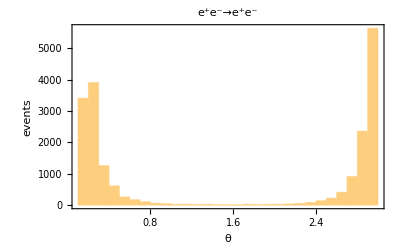

```mathematica
Histogram[thetaList,{0.1},PlotLabel->"e^+e^-→e^+e^-",Frame->True, FrameLabel->{"θ","events"},BaseStyle->{FontSize->14}]
```

Question 8: Where, within the detector, do most of the produced particles end up. Why is this?
Answer: They end up mostly around 0 and pi because they either collide and get a massive deflection (of pi, so 90 degrees) or they miss and get zero.

Now let’s look at ϕ.

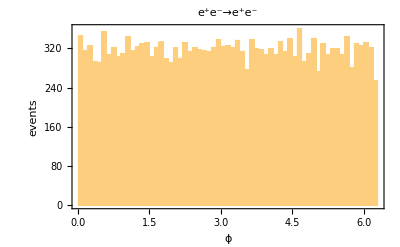

```mathematica
Histogram[phiList,{0.1},PlotLabel->"e^+e^-→e^+e^-", Frame->True, FrameLabel->{"ϕ","events"},BaseStyle->{FontSize->14}]
```

Question 9: What does the ϕ histogram mean about where the particles end up? Is this surprising, why or why not?
Answer: It does not really matter where the particles hit around the center of the cylinder. They hit all over it. It is not very surprising.

Rapidity and
 pseduo-rapidity η
 
 Directive 4: Using the formulae given in class write functions for determining the rapidity and pseudorapidity or a particle from an event. Then for a list of many events.

```mathematica
rapOf[{_,_,_,_,_,_,px_,py_,pz_,e_,___}]:=1/2*Log[(e+pz)/(e-pz)];
etaOf[{_,_,_,_,_,_,px_,py_,pz_,e_,___}]:=-Log[Tan[ArcCos[pz/(√(px^2 + py^2+ pz^2))]/2]];
rap[event_] :=Map[rapOf,event,{1}]//Flatten ;
eta[event_] :=Map[etaOf,event,{1}]//Flatten ;
```

Directive 5: Make histograms of rapidity and pseudorapidity.

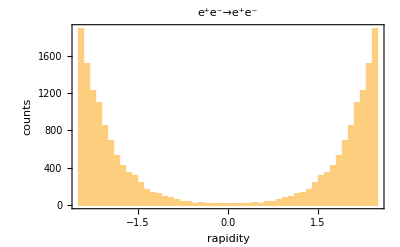

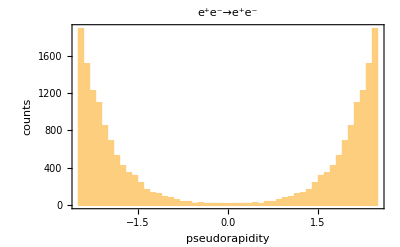

```mathematica
rapList=Flatten[rap/@oeetoeeEvents];
etaList=Flatten[eta/@oeetoeeEvents];
Histogram[rapList,{0.1},PlotLabel->"e^+e^-→e^+e^-", Frame->True, FrameLabel->{"rapidity","counts"},BaseStyle->{FontSize->14}]
Histogram[etaList,{0.1},PlotLabel->"e^+e^-→e^+e^-", Frame->True, FrameLabel->{"pseudorapidity","counts"},BaseStyle->{FontSize->14}]
```

Question 10: How do the two histograms compare and why?
Answer: The two histograms are the same because phi is zero and theta is either zero or pi.
Question 11: How does the shape of the η histogram compare to θ ? What is (approximately) the maximum η that any produced particle attains? Why is that?
Answers: It is similar to theta, but theta has more counts around pi, whereas the rapidity is more evenly distributed. It seems to be about 2.5 because that is where we made the cut. (Remember η < 2.5).

Load the events from the run with η < 5 and make the same rapidity and η plots.

```mathematica
{ioeetoeeη5,oeetoeeη5}=ReadEvents["5n.lhe"];
```

Time taken to read events: 3.76563

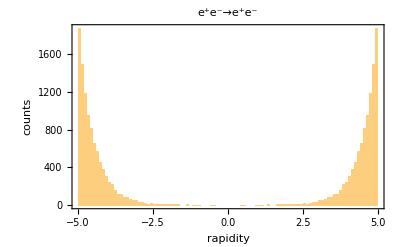

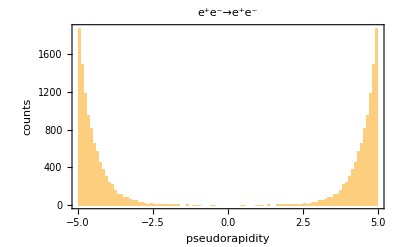

```mathematica
rapListη5=Flatten[rap/@oeetoeeη5];
etaListη5=Flatten[eta/@oeetoeeη5];
Histogram[rapListη5,{0.1},PlotLabel->"e^+e^-→e^+e^-", Frame->True, FrameLabel->{"rapidity","counts"},BaseStyle->{FontSize->14}]
Histogram[etaListη5,{0.1},PlotLabel->"e^+e^-→e^+e^-", Frame->True, FrameLabel->{"pseudorapidity","counts"},BaseStyle->{FontSize->14}]
```

```mathematica
(* Code for Question 12 *)
```

```mathematica
list=Select[etaListη5,-2.5<#<2.5&]
Length[list]
```

{1.99475,-1.99475,2.00926,-2.00926,1.79308,-1.79308,2.35573,-2.35573,1.01836,-1.01836,2.20908,-2.20908,2.4147,-2.4147,2.17014,-2.17014,1.86333,-1.86333,2.38583,-2.38583,1.30712,-1.30712,1.90201,-1.90201,2.26551,-2.26551,1.72189,-1.72189,2.41116,-2.41116,2.30521,-2.30521,0.559486,-0.559486,2.05205,-2.05205,2.46755,-2.46755,2.2528,-2.2528,1.66361,-1.66361,2.41681,-2.41681,0.461388,-0.461388,2.43647,-2.43647,2.44433,-2.44433,1.64289,-1.64289,2.26297,-2.26297,2.31316,-2.31316,2.14454,-2.14454,1.39682,-1.39682,1.78987,-1.78987,1.16668,-1.16668,2.26105,-2.26105,1.88554,-1.88554,2.48394,-2.48394,2.32901,-2.32901,2.4774,-2.4774,2.43357,-2.43357,2.25026,-2.25026,1.78247,-1.78247,1.73452,-1.73452,2.17701,-2.17701,2.04706,-2.04706,1.64323,-1.64323,1.90785,-1.90785,2.10407,-2.10407,2.30785,-2.30785,2.42381,-2.42381,2.2148,-2.2148,2.2251,-2.2251,2.32317,-2.32317,2.29716,-2.29716,0.932283,-0.932283,2.33591,-2.33591,2.31878,-2.31878,2.28847,-2.28847,2.36914,-2.36914,2.0727,-2.0727}

116

```mathematica
(* Code for Question 13 *)
```

```mathematica
N[10000/116]*10000
```

862069.

Question 12: About how many events have |η| < 2.5?
Answer: 116
Question 13: If we keep the generator cut of |η| < 5, about how many events will we need to generate to get about 10,000 events with |η| < 2.5?
Answer: 862069

The take home lesson here is that often one can be prudent about what kind of events are being generated. We want to ensure that the events we are taking the time to simulate are actually the ones we are interested it.

Transverse momentum p_T(and energy)
Directive 5: Define functions that find the transverse momentum and the energy of a given particle. Then write the versions that apply to entire events.

```mathematica
ptOf[{_,_,_,_,_,_,px_,py_,___}]:=Sqrt[px^2+py^2];
enOf[{_,_,_,_,_,_,_,_,_,En_,___}]:=Sqrt[px^2+py^2]/Sin[pz/(√(px^2 + py^2+ pz^2))];
pT[event_]  :=Map[ptOf,event,{1}]//Flatten ;
en[event_]:=Map[enOf,event,{1}]//Flatten ;
```

```mathematica
pTList=Flatten[pT/@oeetoeeEvents];
enList=Flatten[en/@oeetoeeEvents];
pTListη5=Flatten[pT/@oeetoeeη5];
enListη5=Flatten[en/@oeetoeeη5];
```

Directive 6: Make histograms of transverse momentum for both the |η| < 2.5 and |η| < 5 events.

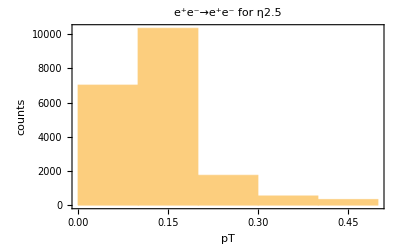

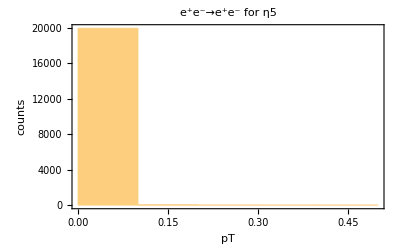

```mathematica
Histogram[pTList,{0.1},PlotLabel->"e^+e^-→e^+e^- for η2.5", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
Histogram[pTListη5,{0.1},PlotLabel->"e^+e^-→e^+e^- for η5", Frame->True, FrameLabel->{"pT","counts"},BaseStyle->{FontSize->14}]
```

Question 14: Explain how and why the two histograms differ.
Answer: The two histograms differ. The one for 2.5 η has most of its events from 0.1 to 0.2 and has a good deal from 0.0 to 0.1. The one for 5 η has about all of its events 20000 at 0.0 to 0.1. They different because the rapidity depends on pz and pT affects pz. (pT is made up of px and py components).

Directive 7: Make a histogram of the energy. Note that it doesn’t really work. Take a look at 50 or so particle energies to see what’s going on

```mathematica
Histogram[enList,{0.1},PlotLabel->"e^+e^-→e^+e^- for η2.5", Frame->True, FrameLabel->{"E","counts"},BaseStyle->{FontSize->14}]
Histogram[enListη5,{0.1},PlotLabel->"e^+e^-→e^+e^- for η5", Frame->True, FrameLabel->{"E","counts"},BaseStyle->{FontSize->14}]
```

-Graphics-

-Graphics-

```mathematica
enList[[1;;50]]
```

{√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))],√(px^2+py^2) Csc[pz/(√(px^2+py^2+pz^2))]}

Question 15: Explain the form of the energy list.
Answer: The energy is always the transverse momentum times the cosecant of theta.

So far we have looked at each particle individually, now lets look at how the two final state particles relate to each other
Δϕ finds the difference in ϕ between two particles

```mathematica
AbsMin[list_]:=Sort[list,Abs[#1]<Abs[#2]&]⟦1⟧;
DeltaPhi[{part1_,part2_}]:=AbsMin[{
(phiOf[part1]-phiOf[part2])
,
(2 π - (phiOf[part1]-phiOf[part2]))
,
(2 π + (phiOf[part1]-phiOf[part2]))
}];
```

Question 16: What do you expect to find when you find the Δϕ of the outgoing electrons?
Answer: I think that it will be 0 due to energy conservation.

```mathematica
DeltaPhiList=Flatten[DeltaPhi/@oeetoeeEvents];
```

Question 17: Were you correct? Either way, comment on the Δϕ results.
Answer: I was right! The answer was pi for every element in the list.

ΔR=√(Δη^2+Δϕ^2)
 is a measure of the angular separation between the particles 
Note that it can be no less that Δϕ

```mathematica
DeltaR[{part1_,part2_}]:=√((etaOf[part1] - etaOf[part2])^2+DeltaPhi[{part1,part2}]^2);
```

Directive 8: Make histograms of ΔR for both the |η| < 2.5 and |η| < 5 events.

```mathematica
DeltaRList=Flatten[DeltaR/@oeetoeeEvents];
DeltaRListη5=Flatten[DeltaR/@oeetoeeη5];
```

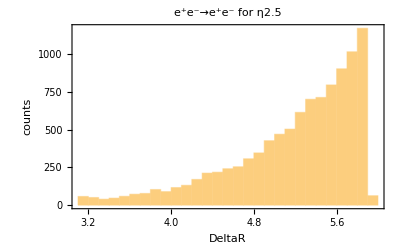

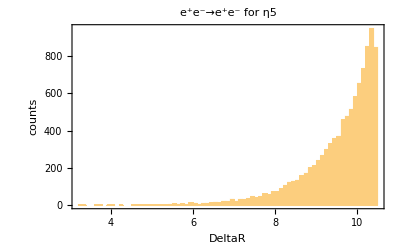

```mathematica
Histogram[DeltaRList,{0.1},PlotLabel->"e^+e^-→e^+e^- for η2.5", Frame->True, FrameLabel->{"DeltaR","counts"},BaseStyle->{FontSize->14}]
Histogram[DeltaRListη5,{0.1},PlotLabel->"e^+e^-→e^+e^- for η5", Frame->True, FrameLabel->{"DeltaR","counts"},BaseStyle->{FontSize->14}]
```

Reflection 3: Comment on the two histograms.
Answer: DeltaR has less counts for its maximum counts for n<5 than for n<2.5. Additionally, DeltaR gets almost twice as great for n<5 than for n<2.5. Neither of them begin showing any data at zero.

Invariant Mass of of two or more objects is obtained by adding the 4-vector of all the particle and asking what the “mass” of the result is

```mathematica
FourVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,En_,___}] := {En, px, py,pz };
FourLength[{En_,px_,py_,pz_}] := Sqrt[En^2 - px^2 - py^2-pz^2];
InvMass[particles_]:= FourLength[ Sum[FourVectorFrom[particles[[i]]],{i,1,Length[particles]}]];
```

Directive 9: Determine the invariant mass of the outgoing particles.

```mathematica
InvMassList=Flatten[InvMass/@oeetoeeEvents];
```

Reflection 4: Comment on the results.
Answer: The invariant mass of the outgoing particles is 1. Which makes sense. All of the outgoing particles should add up to one whole of all their parts.